# Quantum Fourier Transform

The quantum Fourier transform (QFT) is a unitary transformation of quantum states analogous to the discrete Fourier transformation of a finite set of numbers. In the case of quantum Fourier transform, the numbers are replaced with quantum states. The quantum Fourier transformation is a key part of many other quantum algorithms such as the quantum phase estimation, the order-finding problem, the discrete logarithm, and most importantly the hidden subgroup problem. Such a wide range of applications of the quantum Fourier transform stem from the fact that all known quantum algorithms featuring exponential speedup over classical algorithms are variations of the hidden subgroup problem and, as first realized by Kitaev in 1996, the key step to solve the latter problem is the quantum Fourier transform.

The quantum Fourier transform algorithm is illustrated in a circuit.

```mathematica
<<Q3`
```

Symbol S will be used to denote qubits.

```mathematica
Let[Qubit,S]
```

```mathematica
nn=Range[5];
qq=S[nn,None]
```

{S_1,S_2,S_3,S_4,S_5}

Function to handle controlled-rotations.

```mathematica
CR[m_,n_,k_]:=ControlledU[S[m],Phase[2Pi/2^k,S[n]],"Label"->Subscript["R",m]]
```

```mathematica
Let[Integer,j]
jj=j[nn];
jj=Ket/@jj;
```

```mathematica
Clear[v]
v[1]=LogicalForm[Ket[],qq];
```

```mathematica
phase[k_]:=With[
{jj=j[nn]},
Row[{Ket[0],"+",Ket[1],Superscript["e",Row@Join[{"2π"," i ","0","."},Drop[jj,k-1]]]}]
]
ll=Array[phase,5]
v[2]=ProductState[S[nn]->{1,0}]
```

{0+1e^(2π i 0.j_1j_2j_3j_4j_5),0+1e^(2π i 0.j_2j_3j_4j_5),0+1e^(2π i 0.j_3j_4j_5),0+1e^(2π i 0.j_4j_5),0+1e^(2π i 0.j_5)}

(0)_S_1⊗(0)_S_2⊗(0)_S_3⊗(0)_S_4⊗(0)_S_5

Recall that unlike the seemingly general label, the example below is for a particular input.

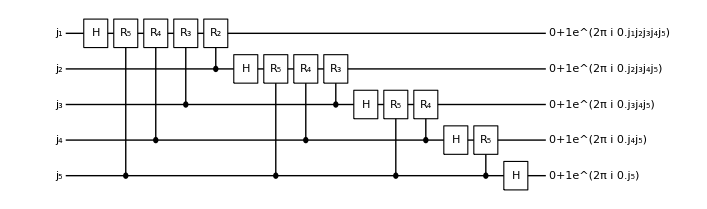

```mathematica
qc=QuantumCircuit[
{v[1],"Label"->jj},
S[1,6],CR[5,1,5],CR[4,1,4],CR[3,1,3],CR[2,1,2],
S[2,6],CR[5,2,4],CR[4,2,3],CR[3,2,2],
S[3,6],CR[5,3,3],CR[4,3,2],
S[4,6],CR[5,4,2],
S[5,6],
{v[2],"Label"->ll},
"PortSize"->{0.65,3}]
```

```mathematica
Timing[ExpressionFor[qc]//LogicalForm[#,qq]&]
```

{0.177255,(0_S_10_S_20_S_30_S_40_S_5)/(4 √2)+(0_S_10_S_20_S_30_S_41_S_5)/(4 √2)+(0_S_10_S_20_S_31_S_40_S_5)/(4 √2)+(0_S_10_S_20_S_31_S_41_S_5)/(4 √2)+(0_S_10_S_21_S_30_S_40_S_5)/(4 √2)+(0_S_10_S_21_S_30_S_41_S_5)/(4 √2)+(0_S_10_S_21_S_31_S_40_S_5)/(4 √2)+(0_S_10_S_21_S_31_S_41_S_5)/(4 √2)+(0_S_11_S_20_S_30_S_40_S_5)/(4 √2)+(0_S_11_S_20_S_30_S_41_S_5)/(4 √2)+(0_S_11_S_20_S_31_S_40_S_5)/(4 √2)+(0_S_11_S_20_S_31_S_41_S_5)/(4 √2)+(0_S_11_S_21_S_30_S_40_S_5)/(4 √2)+(0_S_11_S_21_S_30_S_41_S_5)/(4 √2)+(0_S_11_S_21_S_31_S_40_S_5)/(4 √2)+(0_S_11_S_21_S_31_S_41_S_5)/(4 √2)+(1_S_10_S_20_S_30_S_40_S_5)/(4 √2)+(1_S_10_S_20_S_30_S_41_S_5)/(4 √2)+(1_S_10_S_20_S_31_S_40_S_5)/(4 √2)+(1_S_10_S_20_S_31_S_41_S_5)/(4 √2)+(1_S_10_S_21_S_30_S_40_S_5)/(4 √2)+(1_S_10_S_21_S_30_S_41_S_5)/(4 √2)+(1_S_10_S_21_S_31_S_40_S_5)/(4 √2)+(1_S_10_S_21_S_31_S_41_S_5)/(4 √2)+(1_S_11_S_20_S_30_S_40_S_5)/(4 √2)+(1_S_11_S_20_S_30_S_41_S_5)/(4 √2)+(1_S_11_S_20_S_31_S_40_S_5)/(4 √2)+(1_S_11_S_20_S_31_S_41_S_5)/(4 √2)+(1_S_11_S_21_S_30_S_40_S_5)/(4 √2)+(1_S_11_S_21_S_30_S_41_S_5)/(4 √2)+(1_S_11_S_21_S_31_S_40_S_5)/(4 √2)+(1_S_11_S_21_S_31_S_41_S_5)/(4 √2)}

| Related Guides
▪Quisso Package Guide
▪Q3

| Related Tutorials
▪Quantum Fourier Transform: Semiclassical Implementation
▪QuantumCircuit Usage Examples
▪Quantum Computation and Quantum Information with Q3

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/